```mathematica
Print["#################Variant 7#######################"]
Print["Task 1"]
```

#################Variant 7#######################

Task 1

```mathematica
Plot[(x*Sin[x])^2, {x, -10,10}]
```

⁃Graphics⁃

```mathematica
Print["##############################################"]
Print["Task 2"]
```

##############################################

Task 2

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

```mathematica
F = x^4 / ( 1 + x )^3
```

x^4/(1+x)^3

```mathematica
K = Limit[F/x, x->Infinity]
```

1

```mathematica
B = Limit[F - K*x, x->Infinity]
```

-3

```mathematica
<<Graphics`Legend`
Plot[{F, K*x + B}, {x, -10,10}, AxesLabel-> {"X", "Y"}, PlotStyle->{GrayLevel[0], {GrayLevel[0], Dashing[{0.03}]}}, PlotLabel->"                       График", PlotLegend-> {"График", "Ассимптота"}]
```

⁃Graphics⁃

```mathematica
Print["#############################################"]
Print["Task 3"]
```

##############################################

Task 3

```mathematica
ParametricPlot[{((t+1)^2)/4,((t-1)^2)/4 }, {t, -10,10}]
```

⁃Graphics⁃

```mathematica
Print["#############################################"]
Print["Task 4"]
```

#############################################

Task 4

```mathematica
F = x^2 + y^2 - x /. {x-> R*Cos[fi], y-> R*Sin[fi]}
```

-R Cos[fi]+R^2 Cos[fi]^2+R^2 Sin[fi]^2

```mathematica
K = Solve[F ==0, {R}]
```

{{R→0},{R→Cos[fi]}}

```mathematica
F = {R*Cos[fi],R*Sin[fi]} /. K[[2]]
```

{Cos[fi]^2,Cos[fi] Sin[fi]}

```mathematica
ParametricPlot[{F[[1]], F[[2]]}, {fi, 0, 2*Pi} , AspectRatio->1]
```

⁃Graphics⁃

```mathematica
Print["#############################################"]
Print["Task 5"]
```

#############################################

Task 5

```mathematica
<<Graphics`ImplicitPlot`
```

```mathematica
ImplicitPlot[x^2 + y^2 ==  x + y, {x, -5,5}]
```

⁃Graphics⁃

```mathematica
Print["#############################################"]
Print["Task 6"]
```

#############################################

Task 6

General::obspkg: Graphics`FilledPlot` is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

FilledPlot::shdw: Symbol FilledPlot appears in multiple contexts Graphics`FilledPlot`Global`; definitions in context Graphics`FilledPlot` may shadow or be shadowed by other definitions.

Fills::shdw: Symbol Fills appears in multiple contexts Graphics`FilledPlot`Global`; definitions in context Graphics`FilledPlot` may shadow or be shadowed by other definitions.

Curves::shdw: Symbol Curves appears in multiple contexts Graphics`FilledPlot`Global`; definitions in context Graphics`FilledPlot` may shadow or be shadowed by other definitions.

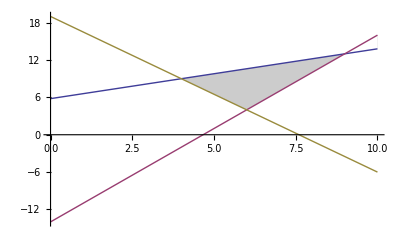

```mathematica
<<Graphics`FilledPlot`
f1 = (4*x + 29)/5;
f2 = -14 + 3*x;
f3 = (38 - 5*x)/2;
FilledPlot[{f1,f2,f3}, {x, -0,10},Fills-> {{{1,2}, GrayLevel[.8]}, {{2,3}, GrayLevel[1]}} , Curves-> Front]
```

```mathematica
Print["#############################################"]
Print["Task 7"]
```

#############################################

Task 7

General::obspkg: Graphics`FilledPlot` is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

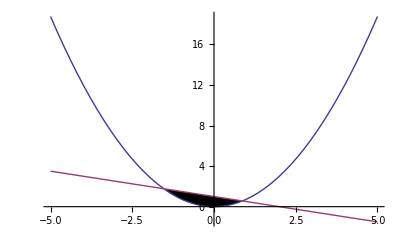

```mathematica
<<Graphics`FilledPlot`;
f1 = 3/4*x^2;
f2 = 1 - 2/4*x;
f3 = 1/(x-2) - 5;

Plot[{f1,f2}, {x,-5,5}, Filling->{1->{{2},{Black,White}}}]
```

```mathematica
⁃Graphics⁃
RegionPlot[f1 , {x, -5,5}, {y, -5,5}]
```

Syntax::noinfo: Input expression contains insufficient information to interpret the result.

```mathematica
Print["#############################################"]
Print["Task 8"]
```

#############################################

Task 8

```mathematica
Plot3D[(-(4*x^2 + 16*y^2 - 16))^(1/2)/2 , {x,-1,1}, {y, -1,1}]
```

-Graphics3D-

```mathematica
Print["#############################################"]
Print["Task 9"]
```

#############################################

Task 9

```mathematica
N[Integrate[If[(x^2 + y^2 + x^2  < 144  && x^2 + y^2 + x^2  > 36 &&  z < ((x^2  y^2)/3)^(1/2) &&  y > x*3^(1/2) && x < x/3^(1/2)),1, 0], {x,-10,10},{y,-20,40},{z,-20,30}]]
RegionPlot3D[ (x^2 + y^2 + x^2  < 144  && x^2 + y^2 + x^2  > 36 &&  z < ((x^2  y^2)/3)^(1/2) &&  y > x*3^(1/2) && x < x/3^(1/2)) , {x,-10,10},{y,-20,40},{z,-20,30}]
```

2998.62

-Graphics3D-

```mathematica
Print["#############################################"]
Print["Task 10"]
```

π

#############################################

Task 10

Task 10

```mathematica
<<Graphics`Animation`
Animate[Plot[t*Sin[x]/x, {x,-15,15}, PlotRange-> {-.25, 1.25}], {t,0.1,1,0.1}]
```